# Euler Problem 7

## 10001st prime

By listing the first six prime numbers: 2, 3, 5, 7, 11, and 13, we can see that the 6th prime is 13.

What is the 10 001st prime number?

## nth Prime By Eratosthenes

Using the nth prime function:

The nth prime is approximated by n*Log[n], but this is necessarily less than the value of the nth prime. So here’s an approximation for the first 100,000 primes:

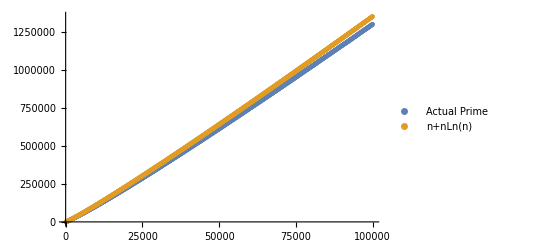

```mathematica
ListPlot[N@Transpose@Table[{{i,Prime[i]},{i,2*i+i*Log[i]}},{i,100,100000,100}],PlotLegends->{"Actual Prime","n+nLn(n)"}]
```

The nth prime function can effectively use this to generate integers:

```mathematica
nthPrimeByEratos[nth_]:=Block[
{
integers=N@Range[2,2*nth+nth*Log[nth]],
primes=2.,
multiples={},
cnt=0
},
While[
cnt<nth,
cnt++;
primes=SelectFirst[Complement[integers,multiples],#>primes&,Break[]];
multiples=Union@Join[multiples,NestWhileList[#+primes&,primes,#<2*nth+nth*Log[nth]&]];
];
{cnt,primes}
]
```

```mathematica
AbsoluteTiming[foo=nthPrimeByEratos[10001];]
```

{39.80294,Null}

```mathematica
foo
```

{10001,104743.}

```mathematica
Prime[10001]
```

104743